# UR5 - Show Matlab Simulation

```mathematica
Clear["Global`*"]
```

Load dynamic from matlab from the following directory: (see also Graphics -> Import .dat files -> importData variable)

```mathematica
directoryMatlab:="C:\\Users\\stefa\\Desktop\\Robotica\\Manipulator - non linear control\\results_simulation\\";
```

```mathematica
thickness:=0.02
```

## Needed

Parameters

### Lengths & Masses

```mathematica
len:={d1->0.089459,d2->0,d3->0,d4->-0.10915,d5->-0.09465,d6->-0.0823,a1->0,a2->-0.425,a3->-0.39225,a4->0,a5->0,a6->0}
mass:={m1->3.7,m2->8.393,m3->2.33,m4->1.219,m5->1.219,m6->0.1879}
```

### Inertia Tensors (here deprecated)

```mathematica
Ip1:={{iP1xx,iP1xy,iP1xz},{iP1yx,iP1yy,iP1yz},{iP1zx,iP1zy,iP1zz}}
Ip2:={{iP2xx,iP2xy,iP2xz},{iP2yx,iP2yy,iP2yz},{iP2zx,iP2zy,iP2zz}}
Ip3:={{iP3xx,iP3xy,iP3xz},{iP3yx,iP3yy,iP3yz},{iP3zx,iP3zy,iP3zz}}
Ip4:={{iP4xx,iP4xy,iP4xz},{iP4yx,iP4yy,iP4yz},{iP4zx,iP4zy,iP4zz}}
Ip5:={{iP5xx,iP5xy,iP5xz},{iP5yx,iP5yy,iP5yz},{iP5zx,iP5zy,iP5zz}}
```

```mathematica
tensorP1:={iP1xx->0.03,iP1xy->0.001,iP1xz->0.001,iP1yx->0.001,iP1yy->0.01,iP1yz->-0.003,iP1zx->0.001,iP1zy->-0.003,iP1zz->0.026}(*link 1*)
```

```mathematica
tensorP2:={iP2xx->0.003,iP2xy->0,iP2xz->0,iP2yx->0,iP2yy->0.003,iP2yz->0,iP2zx->0,iP2zy->0,iP2zz->0.0008}(*link 2*)
```

```mathematica
tensorP3:={iP3xx->0.0017,iP3xy->-0.0003,iP3xz->0,iP3yx->-0.0003,iP3yy->0.001,iP3yz->0,iP3zx->0,iP3zy->0,iP3zz->0.002}(*link 3*)
```

```mathematica
tensorP4:={iP4xx->0.0005,iP4xy->0,iP4xz->0,iP4yx->0,iP4yy->0.0002,iP4yz->0,iP4zx->0,iP4zy->0,iP4zz->0.004}(*link 4*)
```

```mathematica
tensorP5:={iP5xx->0.0007,iP5xy->0,iP5xz->0,iP5yx->0,iP5yy->0.0012,iP5yz->0,iP5zx->0,iP5zy->0,iP5zz->0.0012}(*link 5*)
```

```mathematica
tensors:={tensorP1,tensorP2,tensorP3,tensorP4,tensorP5}
```

```mathematica
robotParameters:={len,tensors,mass}//Flatten
```

Utilities

### Angles Parse

```mathematica
radToDeg[angle_]:=angle/Degree;
degToRad[angle_]:=angle Degree;
```

Build Robot & Env

### Origin & Versor

```mathematica
origin:={0,0,0}
```

```mathematica
versor[scale_]:={Thickness[.005],
Text[Style["x",FontSize->20,Bold,FontColor->Black],{scale+scale/8,0,0}],
Text[Style["y",FontSize->20,Bold,FontColor->Black],{0,scale+scale/8,0}],
Text[Style["z",FontSize->20,Bold,FontColor->Black],{0,0,scale+scale/8}],
,Arrow[{{0,0,0},{scale,0,0}}],Arrow[{{0,0,0},{0,scale,0}}],Arrow[{{0,0,0},{0,0,scale}}]}
```

### Draw End Effector

```mathematica
endEffector[{x_,y_,z_},rotMat_]:={Black,Thickness[thickness],
Line[{
{x,y,z}+rotMat.{0,-0.05,0},
{x,y,z}+rotMat.{0,0.05,0}
}],
Line[{
{x,y,z}+rotMat.{0,-0.05,0},
{x,y,z}+rotMat.{0.1,-0.05,0}
}],
Line[{
{x,y,z}+rotMat.{0,0.05,0},
{x,y,z}+rotMat.{0.1,0.05,0}
}]
}
```

### Distances

```mathematica
P0:=origin;
```

```mathematica
len
```

{d1→0.089459,d2→0,d3→0,d4→-0.10915,d5→-0.09465,d6→-0.0823,a1→0,a2→-0.425,a3→-0.39225,a4→0,a5→0,a6→0}

```mathematica
P1[θ1_]:=RotationMatrix[θ1,{0,0,1}].{0,0,d1}
```

```mathematica
P1P2[θ1_,θ2_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[-θ2,{0,1,0}].{a2,0,0}
```

```mathematica
P2P3[θ1_,θ2_,θ3_,θ4_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[-θ2,{0,1,0}].RotationMatrix[-θ3,{0,1,0}].{a3,0,0}
```

```mathematica
P3P4[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[-θ2,{0,1,0}].RotationMatrix[-θ3,{0,1,0}].RotationMatrix[-θ4,{0,1,0}].{0,d4,0}
```

```mathematica
P4P5[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[-θ2,{0,1,0}].RotationMatrix[-θ3,{0,1,0}].RotationMatrix[-θ4,{0,1,0}].RotationMatrix[-θ5,{0,0,1}].{0,0,d5}
```

```mathematica
P5P6[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[-θ2,{0,1,0}].RotationMatrix[-θ3,{0,1,0}].RotationMatrix[-θ4,{0,1,0}].RotationMatrix[-θ5,{0,0,1}].RotationMatrix[-θ6,{0,1,0}].{0,d6,0}
```

```mathematica
P0P1[θ1_]:=P0+P1[θ1]
```

```mathematica
P0P2[θ1_,θ2_]:=P0P1[θ1]+P1P2[θ1,θ2]
```

```mathematica
P0P3[θ1_,θ2_,θ3_,θ4_]:=P0P2[θ1,θ2]+P2P3[θ1,θ2,θ3,θ4]
```

```mathematica
P0P4[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=P0P3[θ1,θ2,θ3,θ4]+P3P4[θ1,θ2,θ3,θ4,θ5,θ6]
```

```mathematica
P1P4[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=P0P4[θ1,θ2,θ3,θ4,θ5,θ6]-P0P1[θ1]
```

```mathematica
P2P4[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=P0P4[θ1,θ2,θ3,θ4,θ5,θ6]-P0P2[θ1,θ2]
```

```mathematica
P0P5[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=P0P4[θ1,θ2,θ3,θ4,θ5,θ6]+P4P5[θ1,θ2,θ3,θ4,θ5,θ6];
```

```mathematica
P0P6[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=P0P5[θ1,θ2,θ3,θ4,θ5,θ6]+P5P6[θ1,θ2,θ3,θ4,θ5,θ6]
```

### Centers of Mass

```mathematica
P0C1[θ1_]:=RotationMatrix[θ1,{0,0,1}].{-0.01,0.03,0};
```

```mathematica
P1C2[θ1_,θ2_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[θ2,{0,1,0}].{0,0,0.02}
```

```mathematica
P1C3[θ1_,θ2_,θ3_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[θ2,{0,1,0}].RotationMatrix[θ3,{0,1,0}].{0.056,-0.001,0.008}
```

```mathematica
P2C4[θ1_,θ2_,θ3_,θ4_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[θ2,{0,1,0}].RotationMatrix[θ3,{0,1,0}].RotationMatrix[θ4,{1,0,0}].{-0.017,0.04,0}
```

```mathematica
P3C5[θ1_,θ2_,θ3_,θ4_,θ5_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[θ2,{0,1,0}].RotationMatrix[θ3,{0,1,0}].RotationMatrix[θ4,{1,0,0}].RotationMatrix[θ5,{0,1,0}].{0.03,-0.003,-0.02}
```

```mathematica
P3C6[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=RotationMatrix[θ1,{0,0,1}].RotationMatrix[θ2,{0,1,0}].RotationMatrix[θ3,{0,1,0}].RotationMatrix[θ4,{1,0,0}].RotationMatrix[θ5,{0,1,0}].RotationMatrix[θ6,{1,0,0}].{0,0.017,0}
```

```mathematica
P0C2[θ1_,θ2_]:=P0P1[θ1]+P1C2[θ1,θ2]
```

```mathematica
P0C3[θ1_,θ2_,θ3_]:=P0P1[θ1]+P1C3[θ1,θ2,θ3]
```

```mathematica
P0C4[θ1_,θ2_,θ3_,θ4_]:=P0P2[θ1,θ2]+P2C4[θ1,θ2,θ3,θ4]
```

```mathematica
P0C5[θ1_,θ2_,θ3_,θ4_,θ5_]:=P0P3[θ1,θ2,θ3,θ4]+P3C5[θ1,θ2,θ3,θ4,θ5]
```

```mathematica
P0C6[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=P0P3[θ1,θ2,θ3,θ4]+P3C6[θ1,θ2,θ3,θ4,θ5,θ6]
```

### End Effector

```mathematica
rotatedEndEffector[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:=endEffector[P0P6[θ1,θ2,θ3,θ4,θ5,θ6],RotationMatrix[θ1,{0,0,1}].RotationMatrix[-θ2,{0,1,0}].RotationMatrix[-θ3,{0,1,0}].RotationMatrix[-θ4,{0,1,0}].RotationMatrix[-θ5,{0,0,1}].RotationMatrix[-θ6,{0,1,0}].RotationMatrix[-Pi/2,{0,0,1}]]
```

### Draw Manipulator New (UR5)

```mathematica
base:={Red,Thickness[thickness],
Cuboid[origin-origin/4,origin+origin/4]
}
```

```mathematica
shoulderLink[θ1_]:={Yellow,Thickness[thickness],Line[
{
P0,
P0P1[θ1]
}]}
```

```mathematica
upperArmLink[θ1_,θ2_]:={Blue,Thickness[thickness],Line[
{
P0P1[θ1],
P0P2[θ1,θ2]
}
]}
```

```mathematica
forearmLink[θ1_,θ2_,θ3_,θ4_]:={Red,Thickness[thickness],Line[
{
P0P2[θ1,θ2],
P0P3[θ1,θ2,θ3,θ4]
}
]}
```

```mathematica
wrist1Link[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:={Black,Thickness[thickness],Line[
{
P0P3[θ1,θ2,θ3,θ4],
P0P4[θ1,θ2,θ3,θ4,θ5,θ6]
}
]}
```

```mathematica
wrist2Link[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:={Purple,Thickness[thickness],Line[
{
P0P4[θ1,θ2,θ3,θ4,θ5,θ6],
P0P5[θ1,θ2,θ3,θ4,θ5,θ6]
}
]}
```

```mathematica
wrist3Link[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:={Gray,Thickness[thickness],Line[
{
P0P5[θ1,θ2,θ3,θ4,θ5,θ6],
P0P6[θ1,θ2,θ3,θ4,θ5,θ6]
}
]}
```

### Build Manipulator

```mathematica
manipulatorUR5[θ1_,θ2_,θ3_,θ4_,θ5_,θ6_]:={
base,
shoulderLink[θ1],
upperArmLink[θ1,θ2],
forearmLink[θ1,θ2,θ3,θ4],
wrist1Link[θ1,θ2,θ3,θ4,θ5,θ6],
wrist2Link[θ1,θ2,θ3,θ4,θ5,θ6],
wrist3Link[θ1,θ2,θ3,θ4,θ5,θ6],
rotatedEndEffector[θ1,θ2,θ3,θ4,θ5,θ6]
}/.robotParameters
```

## Graphics

Import .dat files

```mathematica
setIimageSize=Medium;
```

```mathematica
importData:={
q1=Transpose[Import[StringJoin[directoryMatlab,"q1.dat"]]]//Flatten;
q2=Transpose[Import[StringJoin[directoryMatlab,"q2.dat"]]]//Flatten;
q3=Transpose[Import[StringJoin[directoryMatlab,"q3.dat"]]]//Flatten;
q4=Transpose[Import[StringJoin[directoryMatlab,"q4.dat"]]]//Flatten;
q5=Transpose[Import[StringJoin[directoryMatlab,"q5.dat"]]]//Flatten;
q6=Transpose[Import[StringJoin[directoryMatlab,"q6.dat"]]]//Flatten;

ξXref=Transpose[Import[StringJoin[directoryMatlab,"xirefX.dat"]]]//Flatten;
ξYref=Transpose[Import[StringJoin[directoryMatlab,"xirefY.dat"]]]//Flatten;
ξZref=Transpose[Import[StringJoin[directoryMatlab,"xirefZ.dat"]]]//Flatten;
ξRref=Transpose[Import[StringJoin[directoryMatlab,"xirefR.dat"]]]//Flatten;
ξPref=Transpose[Import[StringJoin[directoryMatlab,"xirefP.dat"]]]//Flatten;
ξYawref=Transpose[Import[StringJoin[directoryMatlab,"xirefYaw.dat"]]]//Flatten;

ξX=Transpose[Import[StringJoin[directoryMatlab,"xiX.dat"]]]//Flatten;
ξY=Transpose[Import[StringJoin[directoryMatlab,"xiY.dat"]]]//Flatten;
ξZ=Transpose[Import[StringJoin[directoryMatlab,"xiZ.dat"]]]//Flatten;
ξR=Transpose[Import[StringJoin[directoryMatlab,"xiR.dat"]]]//Flatten;
ξP=Transpose[Import[StringJoin[directoryMatlab,"xiP.dat"]]]//Flatten;
ξYaw=Transpose[Import[StringJoin[directoryMatlab,"xiYaw.dat"]]]//Flatten
}
```

Analyze file

```mathematica
fileLen:=q1//Dimensions//First
```

```mathematica
timeOfSimulation:=fileLen;
```

Declaration Functions

### Show and Interact with the Unactuated Model - Function declaration. Use it with: unactuateModel

```mathematica
unactuateModel:=Manipulate[
Column[{
Grid[{
{"EE: ",P0P6[degToRad[θ1],degToRad[θ2],degToRad[θ3],degToRad[θ4],degToRad[θ5],degToRad[θ6]]/.robotParameters}
(*,
{"τr, τl: ",{τrx,τlx}/.{α->αα,τlx->τlxvar,τrx->τrxvar}},
{"ϕ[0]",radToDeg[ϕ[0]]/.solEgoDyn2},
{"θ[0]",radToDeg[θ[0]]/.solEgoDyn2}*)
}
],
Graphics3D[{
versor[0.3],
manipulator[degToRad[θ1],degToRad[θ2],degToRad[θ3],degToRad[θ4],degToRad[θ5],degToRad[θ6]]

},
(*If[robotCondition, PlotRange->{{-0.1,1},{-0.1,1},{-0.1,1}},PlotRange->{{-0.1,2},{-0.1,2},{-0.1,1}}],*)Axes->True,ImageSize->Large,Boxed->False
]
},Alignment->Center
],
{{θ1,0,"θ_1 (deg)"}, -180, 180, Appearance->{"Labeled"}},
{{θ2,-37,"θ_2 (deg)"}, -180, 180, Appearance->{"Labeled"}},
{{θ3,-110,"θ_3 (deg)"}, -180, 180, Appearance->{"Labeled"}},
{{θ4,-2.5,"θ_4 (deg)"}, -180, 180, Appearance->{"Labeled"}},
{{θ5,-1,"θ_5 (deg)"}, -180, 180, Appearance->{"Labeled"}},
{{θ6,55,"θ_6 (deg)"}, -180, 180, Appearance->{"Labeled"}}
(*,{{tt,0,"Time t (sec)"},0,10,Appearance->{"Labeled", "Open"},AnimationRate->1}*)
(*,ContentSize->{800,600}*)
]
```

```mathematica
unactuateModel;
```

### Plot q from Matlab (call importData before calling this function)

```mathematica
plotResults:=Module[{},
GraphicsGrid[
{
{
ListLinePlot[radToDeg[q1], PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time",FontSize->14],Style["q1(t)\n(deg)",FontSize->18]},RotateLabel->False],
ListLinePlot[radToDeg[q2],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time",FontSize->14],Style["q2(t)\n(deg)",FontSize->18]},RotateLabel->False]
},
{
ListLinePlot[radToDeg[q3],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time",FontSize->14],Style["q3(t)\n(deg)",FontSize->18]},RotateLabel->False],
ListLinePlot[radToDeg[q4],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time",FontSize->14],Style["q4(t)\n(deg)",FontSize->18]},RotateLabel->False]
},
{
ListLinePlot[radToDeg[q5],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time",FontSize->14],Style["q5(t)\n(deg)",FontSize->18]},RotateLabel->False],
ListLinePlot[radToDeg[q6],PlotStyle->{Blue},ImageSize->setIimageSize,AspectRatio->1/2,AxesLabel->Automatic,PlotTheme->"Scientific",GridLines->Automatic,FrameLabel->{Style["Time",FontSize->14],Style["q6(t)\n(deg)",FontSize->18]},RotateLabel->False]
}
},Frame->All,Spacings->Scaled[0.15],PlotLabel->Style["Joint positions",FontSize->18]
]
]
```

### Plot EE Desired Trajectory

```mathematica
importData;
```

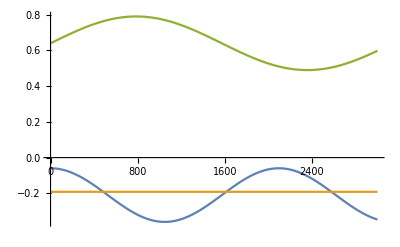

```mathematica
ListLinePlot[{ξXref,ξYref,ξZref}]
```

```mathematica
showDesiredTraj:={Thickness[0.005],Blue,Line[
{{ξXref[[#]],ξYref[[#]],ξZref[[#]]},{ξXref[[#+1]],ξYref[[#+1]],ξZref[[#+1]]}}
]&/@Range[1,Length[ξXref]-1,15]};(*in order to reduce the length of this variable, we take less parameters. 15 means to take just 1 value over 15*)
```

```mathematica
showPartialDesiredTraj[t_]:={Thickness[0.005],Blue,Line[
{{ξXref[[#]],ξYref[[#]],ξZref[[#]]},{ξXref[[#+1]],ξYref[[#+1]],ξZref[[#+1]]}}
]&/@Range[1,t,15]};
```

```mathematica
showEETraj:={Thickness[0.005],Green,Line[
{{ξX[[#]],ξY[[#]],ξZ[[#]]},{ξX[[#+1]],ξY[[#+1]],ξZ[[#+1]]}}
]&/@Range[1,Length[ξX]-1,10]};
```

```mathematica
showPartialTraj[t_]:={Thickness[0.01],Green,Line[
{{ξX[[#]],ξY[[#]],ξZ[[#]]},{ξX[[#+1]],ξY[[#+1]],ξZ[[#+1]]}}
]&/@Range[1,t,10]};
```

```mathematica
Manipulate[Graphics3D[showPartialTraj[t],Axes->True],{{t,1},1,Length[ξXref]-1}];
```

```mathematica
Graphics3D[showEETraj,Axes->True]
```

-Graphics3D-

### Show the 3d Matlab Simulation - Function declaration. Use it with: showMatlabSimulation

```mathematica
showMatlabSimulation:=Module[{},
importData;
{Manipulate[
Column[{
Grid[{
(*{StringJoin["q1: ",ToString[(q1[[tt]]*180/Pi)]," deg"]},
{StringJoin["q2 ",ToString[(q2[[tt]]*180/Pi)]," deg"]},
{StringJoin["q3: ",ToString[(q3[[tt]]*180/Pi)]," deg"]},
{StringJoin["q4: ",ToString[(q4[[tt]]*180/Pi)]," deg"]},
{StringJoin["q5: ",ToString[(q5[[tt]]*180/Pi)]," deg"]},
{StringJoin["q6: ",ToString[(q6[[tt]]*180/Pi)]," deg"]},*)
(*{StringJoin["ξp: ",ToString[(P0P6[q1[[tt]],q2[[tt]],q3[[tt]],q4[[tt]],q5[[tt]],q6[[tt]]]/.robotParameters)]," m"]},*)
{"Blue: desired EE trajectory"},
{"Green: followed EE trajectory"},
{Style[StringJoin["Time: ",ToString[(((tt-1)/100)//N)]," s"],Bold]}
}
],

Graphics3D[{
versor[0.3],
manipulatorUR5[
q1[[tt]],
q2[[tt]],
q3[[tt]],
q4[[tt]],
q5[[tt]],
q6[[tt]]
]
(*,showDesiredTraj*)
,showDesiredTraj
,showPartialTraj[tt]
},
PlotRange->{{-0.7,0.7},{-0.7,0.7},{-0.1,1}},
Axes->True,ImageSize->Large,Boxed->False,(*ViewPoint->{6, -2.5, 1.8}*)(*ViewPoint->Front*)ViewPoint->{1, -2, 1.1}
]

},Alignment->Center
],
{{tt,1,"Time t (sec)"},1,fileLen,1,Appearance->{"Labeled", "Open"},AnimationRate->100,RefreshRate->60}
(*,ContentSize->{800,600}*)
],
plotResults
}
]
```

3D Visualizer

```mathematica
unactuateModel;
```

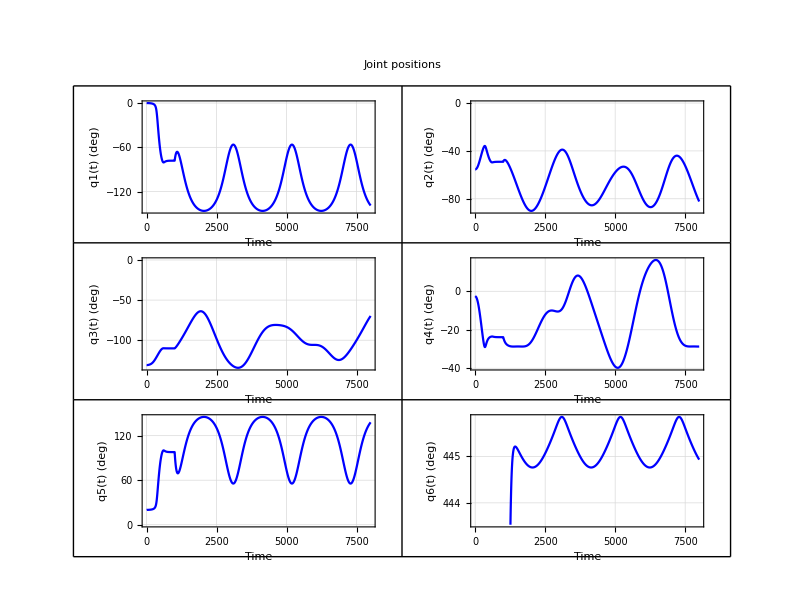

```mathematica
showMatlabSimulation
```